```mathematica
Export["file.ext",expr]
```

```mathematica
Export["gamme.wav",Sound[Table[SoundNote[k-6],{k,0,11}],3]]
```

Export::nodta: Sound[{SoundNote[-6], SoundNote[-5], SoundNote[-4], SoundNote[-3], SoundNote[-2], SoundNote[-1], SoundNote[0], SoundNote[1], SoundNote[2], SoundNote[3], « 2 »}, 3] contains no data that can be exported to the WAV format.

$Failed

```mathematica
EmitSound[Table[SoundNote[k-6],{k,0,11}],3]
```

EmitSound[{SoundNote[-6],SoundNote[-5],SoundNote[-4],SoundNote[-3],SoundNote[-2],SoundNote[-1],SoundNote[0],SoundNote[1],SoundNote[2],SoundNote[3],SoundNote[4],SoundNote[5]},3]

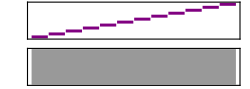

```mathematica
Sound[Table[SoundNote[k-6],{k,0,11}],3]
```

```mathematica
Clear[a];a[n_?EvenQ]:=a[n]=-a[n/2];a[0]=0;a[n_]:=a[n]=a[(n-1)/2]+1;Table[a[n],{n,0,99}]
```

{0,1,-1,2,1,0,-2,3,-1,2,0,1,2,-1,-3,4,1,0,-2,3,0,1,-1,2,-2,3,1,0,3,-2,-4,5,-1,2,0,1,2,-1,-3,4,0,1,-1,2,1,0,-2,3,2,-1,-3,4,-1,2,0,1,-3,4,2,-1,4,-3,-5,6,1,0,-2,3,0,1,-1,2,-2,3,1,0,3,-2,-4,5,0,1,-1,2,1,0,-2,3,-1,2,0,1,2,-1,-3,4,-2,3,1,0}

```mathematica
Table[a[2^k],{k,0,9}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1}

```mathematica
Table[a[2^k-1],{k,0,9}]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
Table[a[2^k+1],{k,0,9}]
```

{-1,2,0,2,0,2,0,2,0,2}

```mathematica
Table[a[2^k-2],{k,1,9}]
```

{0,-1,-2,-3,-4,-5,-6,-7,-8}

```mathematica
Table[a[2^k-3],{k,2,9}]
```

{1,0,-1,-2,-3,-4,-5,-6}

```mathematica
Table[a[k^2],{k,0,9}]
```

{0,1,1,2,1,3,2,-1,1,1}

```mathematica
FindSequenceFunction[Table[a[n],{n,100}],n]
```

FindSequenceFunction[{1,-1,2,1,0,-2,3,-1,2,0,1,2,-1,-3,4,1,0,-2,3,0,1,-1,2,-2,3,1,0,3,-2,-4,5,-1,2,0,1,2,-1,-3,4,0,1,-1,2,1,0,-2,3,2,-1,-3,4,-1,2,0,1,-3,4,2,-1,4,-3,-5,6,1,0,-2,3,0,1,-1,2,-2,3,1,0,3,-2,-4,5,0,1,-1,2,1,0,-2,3,-1,2,0,1,2,-1,-3,4,-2,3,1,0,3},n]

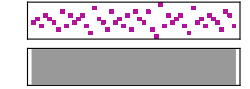

```mathematica
Sound[Table[SoundNote[a[k],0.5,"Harpsichord"],{k,0,49}]]
```

```mathematica
Export["norgard.mid",Sound[Table[SoundNote[a[k],0.5,"Harpsichord"],{k,0,49}]]]
```

norgard.mid

```mathematica
Export["midlle.mid",Sound[{SoundNote["C"],SoundNote["G"]}]]
```

midlle.mid

-Graphics-

```mathematica
Click for copyable input
```

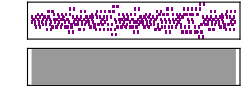

```mathematica
Sound[Table[SoundNote[{a[k],a[k+3]}],{k,0,150}],30]
```

```mathematica
Table[SoundNote[k-6],{k,0,11}]
```

{SoundNote[-6],SoundNote[-5],SoundNote[-4],SoundNote[-3],SoundNote[-2],SoundNote[-1],SoundNote[0],SoundNote[1],SoundNote[2],SoundNote[3],SoundNote[4],SoundNote[5]}

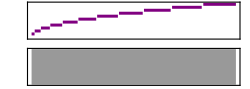

```mathematica
Sound[Table[SoundNote[k-6,k],{k,0,11}],3]
```

```mathematica
lst=
```

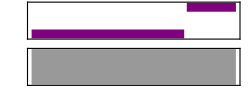

```mathematica
Sound[SoundNote@@@{{0,3},{3,1}}]
```

```mathematica
t=0.33;
```

```mathematica
notes={0,0,0,2,4,2,0,4,2,2,0}-6;durées={t,t,t,t,2t,2t,t,t,t,t,4t};
```

```mathematica
notes={0,0,2,2,4,4,2,2,7,7,9,9}-6;durées=Table[0.5,{i,12}];
```

```mathematica
Transpose[{notes,durées}]
```

{{-6,0.5},{-6,0.5},{-4,0.5},{-4,0.5},{-2,0.5},{-2,0.5},{-4,0.5},{-4,0.5},{1,0.5},{1,0.5},{3,0.5},{3,0.5}}

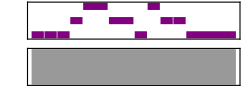

```mathematica
Sound[SoundNote@@@Transpose[{notes,durées}]]
```

```mathematica
melodie=Transpose[{notes,durées}]
```

{{9,0.33},{12,0.33},{15,0.33},{6,0.33},{17,0.33},{10,0.33},{8,0.33},{11,0.33},{14,0.33},{16,0.33},{7,0.33},{13,0.33}}

```mathematica
Sound
```

```mathematica
m=SoundNote@@@melodie/.t->0.33
```

melodie

```mathematica
notes=Transpose[melodie][[1]]
```

{-6,-6,-6,-4,-2,-4,-6,-2,-4,-4,-6}

```mathematica
durées=Transpose[melodie][[2]]
```

{0.33,0.33,0.33,0.33,0.66,0.66,0.33,0.33,0.33,0.33,1.32}

```mathematica
mmiror=SoundNote@@@Transpose[{6-notes,durées}]
```

{SoundNote[12,0.33],SoundNote[12,0.33],SoundNote[12,0.33],SoundNote[10,0.33],SoundNote[8,0.66],SoundNote[10,0.66],SoundNote[12,0.33],SoundNote[8,0.33],SoundNote[10,0.33],SoundNote[10,0.33],SoundNote[12,1.32]}

```mathematica
mrev=SoundNote@@@Transpose[{Reverse[notes],Reverse[durées]}]
```

{SoundNote[-6,1.32],SoundNote[-4,0.33],SoundNote[-4,0.33],SoundNote[-2,0.33],SoundNote[-6,0.33],SoundNote[-4,0.66],SoundNote[-2,0.66],SoundNote[-4,0.33],SoundNote[-6,0.33],SoundNote[-6,0.33],SoundNote[-6,0.33]}

```mathematica
mmirrorrev=SoundNote@@@Transpose[{Reverse[6-notes],Reverse[durées]}]
```

{SoundNote[12,1.32],SoundNote[10,0.33],SoundNote[10,0.33],SoundNote[8,0.33],SoundNote[12,0.33],SoundNote[10,0.66],SoundNote[8,0.66],SoundNote[10,0.33],SoundNote[12,0.33],SoundNote[12,0.33],SoundNote[12,0.33]}

```mathematica
Sound[m]
```

Sound[melodie]

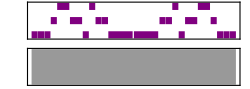

```mathematica
Sound[{m,mrev},{0,5.28}]
```

```mathematica
l1={-6,-6,-6,-4,-2,-4,-6,-2,-4,-4,-6}
```

{-6,-6,-6,-4,-2,-4,-6,-2,-4,-4,-6}

```mathematica
Transpose[{l1,l2}]
```

{{-6,0},{-6,0},{-6,0},{-4,-2},{-2,-4},{-4,-2},{-6,0},{-2,-4},{-4,-2},{-4,-2},{-6,0}}

```mathematica
l2=-4-{-6,-6,-6,-4,-2,-4,-6,-2,-4,-4,-6}
```

{2,2,2,0,-2,0,2,-2,0,0,2}

```mathematica
l3=Reverse[l1]
```

{-6,-4,-4,-2,-6,-4,-2,-4,-6,-6,-6}

```mathematica
Transpose[{Transpose[{l1,l2}],durées}]
```

{{{-6,0},0.33},{{-6,0},0.33},{{-6,0},0.33},{{-4,-2},0.33},{{-2,-4},0.66},{{-4,-2},0.66},{{-6,0},0.33},{{-2,-4},0.33},{{-4,-2},0.33},{{-4,-2},0.33},{{-6,0},1.32}}

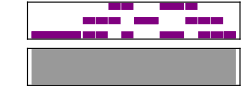

```mathematica
Sound[SoundNote@@@Transpose[{Transpose[{l1,l3}],durées}]/.t->0.33]
```

```mathematica
Sound[Table[SoundNote[k-6],{k,0,11}],3]
```

-Graphics-

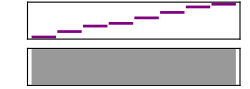

```mathematica
Sound[Part[Table[SoundNote[k-6],{k,0,12}],{1,3,5,6,8,10,12,13}],3]
```

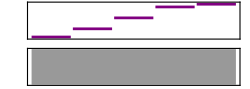

```mathematica
Sound[Part[Table[SoundNote[k-6],{k,0,12}],{1,4,8,12,13}],3]
```